# Routhians E’(ω)

## The energy in the rotating frame

Calculating the experimental and theoretical Routhians E’(ω) for ^163Lu
The Routhian: energy of a state I with given ω in the rotating frame of reference

### Experimental data

```mathematica
spins1=Table[i,{i,6.5,48.5,2}];
spins2=Table[i,{i,13.5,45.5,2}];
spins3=Table[i,{i,16.5,42.5,2}];
spins4=Table[i,{i,23.5,41.5,2}];
E0=1.7399;
expEn1={{6.5,0},{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD1Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn1];
expEn2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD2Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn2];
expEn3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
TSD3Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn3];
expEn4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
TSD4Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn4];
```

### Fit parameters: numerical values from CXX (imported)

```mathematica
a1=1/(2*72);a2=1/(2*15);a3=1/(2*7);v=2.1;gm=22;shiftTSD2=0.3;shiftTSD4=0.6;
```

### Analytic formulas for the excitation energies

```mathematica
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)/2(I+j)+A1(I-j)^2-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B1[I,j,A1,A2,A3,V,γ]-(B1[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B1[I,j,A1,A2,A3,V,γ]+(B1[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
EWobb[n1_,n2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](n1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](n2+1/2);
IF[I_]:=1/(2I);
TSD1[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD2[I_,A1_,A2_,A3_,V_,γ_,shift_]:=(EWobb[0,0,I,6.5,A1,A2,A3,V,γ]+shift)-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD3[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD4[I_,A1_,A2_,A3_,V_,γ_,shift_]:=(EWobb[0,0,I,6.5,A1,A2,A3,V,γ]+shift)-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
```

### Wobbling bands used in 2ϵ-fit

```mathematica
band1[I_]:=TSD1[I,a1,a2,a3,v,gm];
band2[I_]:=TSD2[I,a1,a2,a3,v,gm,shiftTSD2];
band3[I_]:=TSD3[I,a1,a2,a3,v,gm];
band4[I_]:=TSD4[I,a1,a2,a3,v,gm,shiftTSD4];
```

## The Rotational Frequency

Notation: hrot -> ℏω

```mathematica
(*Experimental determination for the rotational frequency*)
hrotExp[band_,Iidx_]:=1/2*(band[[Iidx,2]]-band[[Iidx-1,2]]);
hrotDataExp[band_]:=Table[{band[[i,1]],hrotExp[band,i]},{i,2,Length[band]}];
(*Theoretical determination for the rotational frequency*)
hrotTh[band_,I_]:=1/2(band[I]-band[I-2]);
hrotThData[band_,spins_]:=Table[{spins[[i]],hrotTh[band,spins[[i]]]},{i,2,Length[spins]}];
(*generate the data in a tabular form*)
hrot1Exp=hrotDataExp[TSD1Exp];
hrot2Exp=hrotDataExp[TSD2Exp];
hrot3Exp=hrotDataExp[TSD3Exp];
hrot4Exp=hrotDataExp[TSD4Exp];
hrot1Th=hrotThData[band1,spins1];
hrot2Th=hrotThData[band2,spins2];
hrot3Th=hrotThData[band3,spins3];
hrot4Th=hrotThData[band4,spins4];
```

## The Routhian

```mathematica
j[I_]:=I-1/2;
(*the experimental routhian*)
eRouthExp[band_,Iidx_]:=1/2*(band[[Iidx,2]]+band[[Iidx-1,2]])-hrotExp[band,Iidx]*j[band[[Iidx,1]]];
(*the theoretical routhian*)
eRouthTh[band_,I_]:=1/2*(band[I]+band[I-2])-hrotTh[band,I]*j[I];
```

### Function of ℏω -> eRouth1

```mathematica
(*generate the data in a tabular form*)
eRouth1DataExp[band_]:=Table[{QQ,QQ},{i,2,Length[band]}];
eRouth1DataTh[band_,spins_]:=Table[{hrotTh[band,spins[[i]]],eRouthTh[band,spins[[i]]]},{i,2,Length[spins]}];
```

### Function of spin I -> eRouth2

```mathematica
(*generate the data in a tabular form*)
eRouth2DataExp[band_]:=Table[{QQ,QQ},{i,2,Length[band]}];
eRouth2DataTh[band_,spins_]:=Table[{QQ,QQ},{i,2,Length[spins]}];
```

### Compute the reference energy from the total Routhian

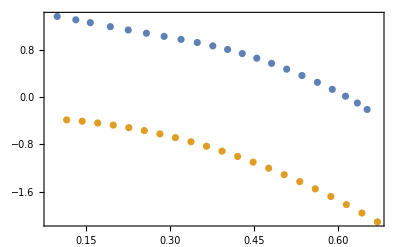

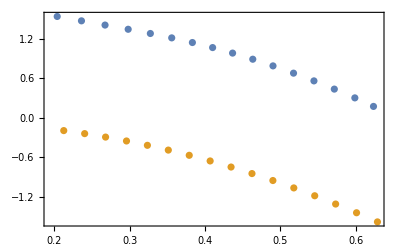

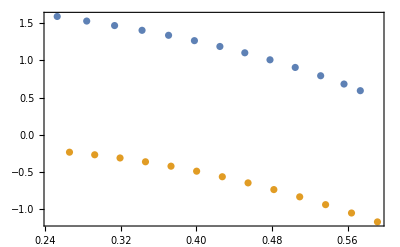

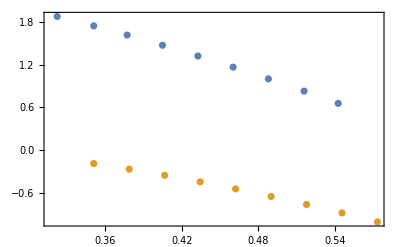

```mathematica
reference[data_]:=Map[Function[x,{x[[1]],x[[2]]+x[[1]]^2*31.7}],data];
frout1=eRouthDataExp[TSD1Exp];
frout11=eRouthDataTh[band1,spins1];
frout2=eRouthDataExp[TSD2Exp];
frout22=eRouthDataTh[band2,spins2];
frout3=eRouthDataExp[TSD3Exp];
frout33=eRouthDataTh[band3,spins3];
frout4=eRouthDataExp[TSD4Exp];
frout44=eRouthDataTh[band4,spins4];
(*ListPlot[{reference[frout1],reference[frout11]},PlotRange->Full,Frame->True,Axes->False]
ListPlot[{reference[frout2],reference[frout22]},PlotRange->Full,Frame->True,Axes->False]
ListPlot[{reference[frout3],reference[frout33]},PlotRange->Full,Frame->True,Axes->False]
ListPlot[{reference[frout4],reference[frout44]},PlotRange->Full,Frame->True,Axes->False]*)
```

```mathematica
(*ListPlot[{eRouthDataTh[band1,spins1],eRouthDataExp[TSD1Exp]},Joined->True,PlotMarkers->{Automatic, Medium}]
ListPlot[{eRouthDataTh[band2,spins2]},Joined->True,PlotMarkers->{Automatic, Medium}]
ListPlot[{eRouthDataTh[band3,spins3]},Joined->True,PlotMarkers->{Automatic, Medium}]
ListPlot[{eRouthDataTh[band4,spins4]},Joined->True,PlotMarkers->{Automatic, Medium}]*)
```